## perimeterLength-example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m;
```

Cellzilla2D (3.0.51e (11 June 2017)) loaded Mon 12 Jun 2017 13:43:28
using xCellerator 0.95 and XSSA 1.3.2
GPL License Terms Apply

```mathematica
polygon={{0.6656821861024209,0.5885139068629628},{0.3674265409089722,0.548792012192189},{-0.5083022778120968,0.03200749861905844},{-0.9625187848327785,-0.40634552703524995},{-0.603944818863048,-0.6296344493677282},{-0.2938861906733466,-0.19134629851828722},{0.3771323695082593,0.14124017268253336}};
```

```mathematica
perimeterLength[polygon]
```

4.18945

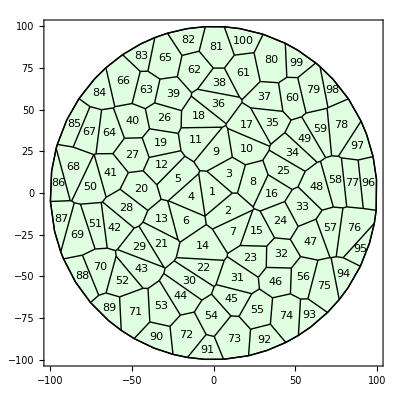

```mathematica
w=TemplateRandomCircularGrid[100,100];
ShowTissue[w,"CellNumbers"->True, Frame-> True]
```

```mathematica
perimeterLength[w,1]
```

73.8568

```mathematica
perimeters=perimeterLength[w]
```

{73.8568,76.7389,68.1635,74.9057,77.3241,75.1355,76.292,72.0389,77.6051,75.1717,77.2903,68.9015,70.5313,84.9876,69.3267,68.466,79.6841,76.6045,67.8086,73.0439,78.1849,77.7827,70.3637,70.3375,73.2929,67.9947,67.7691,73.8336,79.2932,79.2234,76.0542,65.7331,68.0792,76.1042,71.7928,79.2703,71.9234,68.886,68.1197,70.1998,74.0048,76.53,81.0961,75.0175,67.3349,66.3585,75.9309,77.6033,76.3922,80.8744,76.2475,72.2521,74.8962,69.5693,69.6977,70.6106,77.5256,80.3341,77.8053,69.4451,77.2465,70.3679,63.3551,75.3352,77.3871,82.2632,75.254,90.1358,87.7883,78.3334,81.7202,77.0828,77.687,79.1282,82.9444,90.381,79.3743,87.7593,78.3714,82.4052,74.8851,65.605,62.3122,72.9719,75.0841,76.9258,76.6008,75.5945,65.3212,68.9718,59.9228,67.1431,63.5089,68.7272,67.0492,79.0225,69.6136,64.7844,63.305,66.8629}

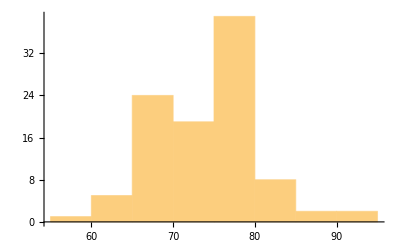

```mathematica
Histogram[perimeterLength[w]]
```

```mathematica
areas=areafunction[w]
```

{286.129,328.734,281.37,270.435,345.915,304.599,297.648,314.144,337.136,327.847,330.901,266.887,268.964,430.029,283.517,278.101,323.633,310.784,294.325,358.228,322.079,275.66,302.569,322.391,321.735,305.192,324.984,324.355,284.313,313.21,345.668,300.809,301.171,309.629,290.879,329.963,318.135,246.818,317.315,336.603,328.94,304.055,335.713,292.103,269.1,305.212,372.567,345.391,291.314,328.532,278.297,280.425,343.021,325.119,332.925,307.253,312.318,324.734,292.757,303.416,387.42,338.505,259.96,330.864,403.901,430.139,293.742,398.714,408.191,358.022,427.729,406.678,418.061,414.16,405.527,439.844,294.509,441.038,360.474,453.828,386.711,252.813,208.017,305.089,268.327,213.254,245.109,271.203,231.576,275.477,195.477,266.353,212.147,241.925,170.418,283.271,258.609,177.907,221.55,259.497}

Calculate an isoperimetric ratio A/L^2; for a circle, 1/4Pi = 0.0796; for a square, 1/16=0.0625; according to the isoperimetric inequality, A/L^2 <= 4Pi

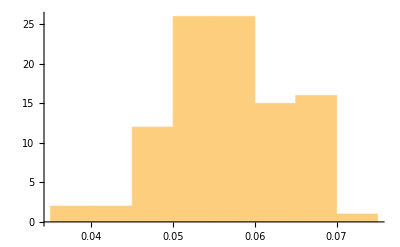

```mathematica
Histogram[areas/perimeters^2]
```